```mathematica
n=2;
∑_(k=0)^(n-1) (Subscript[V, k] Log[(∑_(i=0)^k Subscript[m, 2i]+x)/(∑_(j=1)^(k+1) Subscript[m, 2j-1]+x)])
Manipulate[∑_(k=0)^(n-1) (Subscript[V, k] Log[(∑_(i=0)^k Subscript[m, 2i]+x)/(∑_(j=1)^(k+1) Subscript[m, 2j-1]+x)]),{n,1,10,1}]
```

Log[(x+m_0)/(x+m_1)] V_0+Log[(x+m_0+m_2)/(x+m_1+m_3)] V_1

```mathematica
Log[(x+Subscript[m, 0])/(x+Subscript[m, 1])] Subscript[V, 0]+Log[(x+Subscript[m, 0]+Subscript[m, 2])/(x+Subscript[m, 1]+Subscript[m, 3])] Subscript[V, 1]==V
```

```mathematica
Manipulate[Plot[Log[(x+Subscript[m, 0])/(x+Subscript[m, 1])] Subscript[V, 0]+Log[(x+Subscript[m, 0]+Subscript[m, 2])/(x+Subscript[m, 1]+Subscript[m, 3])] Subscript[V, 1],{x,-8,8}],{Subscript[m, 0],0,10},{Subscript[m, 1],0,10},{Subscript[m, 2],0,10},{Subscript[m, 3],0,10},{Subscript[V, 0],0,100},{Subscript[V, 1],0,100}]
```

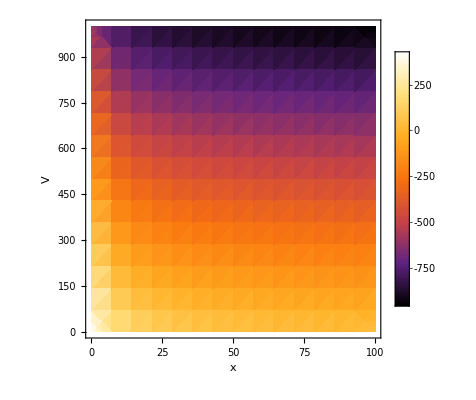

```mathematica
DensityPlot[Log[(x+10)/(x+4)] 317+Log[(x+22)/(x+14)]304==V,{x,0,100},{V,0,1000},ColorFunction->"SunsetColors",PlotLegends->Automatic,ExclusionsStyle->Red,Axes->True,AxesLabel->Automatic,(*MeshFunctions->{Norm[{#1,#2,#3}]&},Mesh->10,*)PlotRange->All,WorkingPrecision->1000,ClippingStyle->Automatic]
```

```mathematica
|
```

```mathematica
A==B Log[(a+x)/(b+x)]
```

```mathematica
A==B Log[(a+x)/(b+x)]
(b(2  Subscript[m, 1]+ Subscript[m, 3])-(2 Subscript[m, 0]+Subscript[m, 2]))^2
```

A==B Log[(a+x)/(b+x)]

(-2 m_0-m_2+b (2 m_1+m_3))^2

```mathematica
Simplify[(-2 Subscript[m, 0]-Subscript[m, 2]+b (2 Subscript[m, 1]+Subscript[m, 3]))^2]
```

(2 m_0-2 b m_1+m_2-b m_3)^2

```mathematica
Expand[(2 Subscript[m, 0]-2 b Subscript[m, 1]+Subscript[m, 2]-b Subscript[m, 3])^2]
```

4 m_0^2-8 b m_0 m_1+4 b^2 m_1^2+4 m_0 m_2-4 b m_1 m_2+m_2^2-4 b m_0 m_3+4 b^2 m_1 m_3-2 b m_2 m_3+b^2 m_3^2

```mathematica
Simplify[%10]
```

(2 m_0-2 b m_1+m_2-b m_3)^2

```mathematica
Simplify[-2 Subscript[m, 0]-Subscript[m, 2]+b (2 Subscript[m, 1]+Subscript[m, 3])]
```

-2 m_0+2 b m_1-m_2+b m_3

```mathematica
Solve[A==B Log[(a+x)/(b+x)],{x},Reals]
Solve[V==B Log[(Subscript[m, 0]+x)/(Subscript[m, 1]+x)]+B Log[(Subscript[m, 0]+Subscript[m, 2]+x)/(Subscript[m, 1]+Subscript[m, 3]+x)]+B Log[(Subscript[m, 0]+Subscript[m, 2]+Subscript[m, 4]+x)/(Subscript[m, 1]+Subscript[m, 3]+Subscript[m, 5]+x)],x,Complexes]
```

{{x→(-a+b ⅇ^(A/B))/(1-ⅇ^(A/B))}}

```mathematica
Solve[∑_(k=0)^(n-1) (Subscript[V, k] Log[(∑_(i=0)^k Subscript[m, 2i]+x)/(∑_(j=1)^(k+1) Subscript[m, 2j-1]+x)]),x]
```

Solve::naqs: ∑_(k=0)^(-1+n) Log[(x+∑_(i=0)^k m_Times[«2»])/(x+Sum[Subscript[«2»],{«3»}])] V_k is not a quantified system of equations and inequalities.

```mathematica
Solve[V==B*Log[(m0+x)/(m1+x)]+B*Log[(m0+m2+x)/(m1+m3+x)]+B*Log[(m0+m2+m4+x)/(m1+m3+m5+x)]+B*Log[(m0+m2+m4+m6+x)/(m1+m3+m5+m7+x)],x,Complexes]
```

```mathematica
ComplexPlot3D[355*9.81*Log[(8400+z)/(8400-6428+z)]+310*9.81*Log[(25828-8400+z)/((25828-8400)-17427+z)],{z,-40000-40000I,40000+40000I},
PlotLegends->Automatic,Mesh->20,
PlotRange->Full,
MeshStyle->{Black,White}]
```

-Graphics3D-

```mathematica
Manipulate[(∑_(i=0)^k ((k-i) Subscript[m, 2i])-β∑_(i=1)^k (k Subscript[m, 2i-1]))/(k(β-1)),{k,1,10,1}]
```

```mathematica
Manipulate[Simplify[(∑_(i=0)^k -((k-i) Subscript[m, 2i])+∑_(i=1)^k ((k-i+1) β Subscript[m, 2i-1]))^2],{k,2,10,1}]
```

```mathematica
Manipulate[(∑_(n=0)^(p-1) ( Subscript[m, 2n])-β∑_(n=1)^p ( Subscript[m, 2n-1]))/(p(β-1)),{p,1,10,1},Dynamic[p]]
```

```mathematica
Manipulate[∑_(n=0)^(p-1) (Subscript[m, n] Subscript[M, 2n+1]),{p,1,10,1},Dynamic[p]]
```

```mathematica
Manipulate[∑_(n=2)^p (Subscript[M, 2n](∑_(k=0)^(n-1) (Subscript[m, 2k]))),{p,2,4,1},Dynamic[p]]
```

```mathematica
Manipulate[(∑_(k=0)^(p-1) (Subscript[m, 2k])),{p,2,4,1},Dynamic[p]]
```

```mathematica
Manipulate[∑_(n=2)^p (β Subscript[M, 2n+1](∑_(k=0)^(n-1) (Subscript[m, 2k+1]))),{p,2,4,1},Dynamic[p]]
```

```mathematica
Manipulate[∑_(n=2)^p (Subscript[M, 2n](∑_(k=0)^(n-1) (Subscript[m, 2k])))+∑_(n=2)^p (β Subscript[M, 2n+1](∑_(k=0)^(n-1) (Subscript[m, 2k+1]))),{p,1,5,1},Dynamic[p]]
```

```mathematica
Manipulate[
Normal[1/(p(β-1))((∑_(n=0)^(p-1) ( Subscript[m, 2n])-β∑_(n=1)^p ( Subscript[m, 2n-1]))((-(∑_(n=0)^(p-1) ( Subscript[m, 2n])-β∑_(n=1)^p ( Subscript[m, 2n-1]))^2+p(β-1)(∑_(n=2)^p (Subscript[M, 2n](∑_(k=0)^(n-1) (Subscript[m, 2k])))+∑_(n=2)^p (β Subscript[M, 2n+1](∑_(k=0)^(n-1) (Subscript[m, 2k+1])))))))^(1/3)],
{p,1,10,1},
Dynamic[p]
]
```